# Test packing

```mathematica
SetCurrentDir[]
```

C:\HY-Data\AIPENTTI\Progs\PSR-Programs\APprogs\dev\packingproperties\

```mathematica
sph = Import[ "pack.geom", "Table"];
sph[[1]]
Length[sph]
```

{2.56436,1.85132,3.70883,0.5}

48

```mathematica
Graphics3D[ Map[ Sphere[ #[[{1,2,3}]], #[[4]]] &, sph], Axes->True]
```

```mathematica
per = 5.0;
sphp = Flatten[ Table[ Map[ #+{per ix,per iy,per iz, 0} &, sph], {ix, -1, 1}, {iy, -1, 1}, {iz, -1, 1}], 3];
sphp[[1]]
Length[sphp]
```

{-2.43564,-3.14868,-1.29117,0.5}

1296

```mathematica
Graphics3D[ Map[ Sphere[ #[[{1,2,3}]], #[[4]]] &, sphp], Axes->True]
```

```mathematica
t = Import[ "pack.out", "Table"];
n = t[[1,3]]
```

573

```mathematica
nnd = Flatten[ Take[ t, {6, n+6-1}]];
nnd[[1]]
```

0.0222154

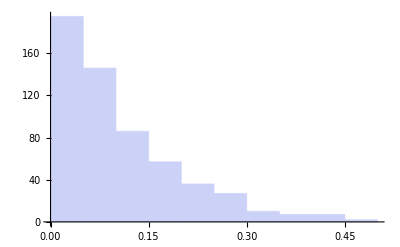

```mathematica
Histogram[ nnd/0.5]
```